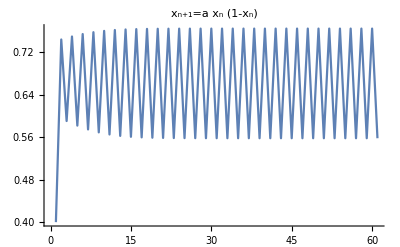

```mathematica
x0=0.4;
a=3.1;
X={x0};
For[i=1,i≤60,i++,x1=a*x0*(1-x0);AppendTo[X,x1];x0=x1]
ListLinePlot[X,DataRange->All, PlotRange->All, PlotLabel->HoldForm[Subscript[x,n+1]=a*Subscript[x,n](1-Subscript[x,n])]]
```

```mathematica
Manipulate[x0=0.4;X={x0};For[i=1,i≤60,i++,x1=a*x0*(1-x0); AppendTo[X,x1]; x0=x1];
ListLinePlot[X,DataRange->All, PlotRange->{0,1},PlotLabel->Subscript[x,n+1]== a*Subscript[x,n](1-Subscript[x,n])],{a,1,4}]
```

```mathematica
Manipulate[X={};x0=0.4;For[i=1,i≤60,i++,x1=a*x0*(1-x0);  x0=x1];
For[i=1,i≤60,i++,x1=a*x0*(1-x0);AppendTo[X,{a,x1}];x0=x1];
ListPlot[X, PlotRange->{{1,4.1},{0,1}}],{a,1,4}]
```

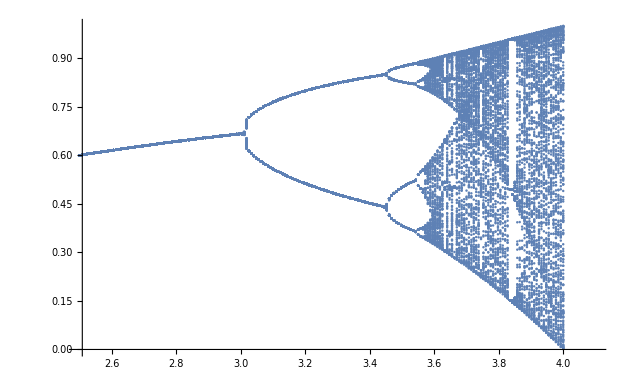

```mathematica
X={};
x0=0.4;a0 = 3.5;K = 200; PN = 200;
For[k=0,k≤K,k++,a=a0+k*(4-a0)/K;
For[i=1,i≤60,i++,x1=a*x0*(1-x0);  x0=x1];
For[i=61,i≤(PN+61),i++,x1=a*x0*(1-x0);AppendTo[X,{a,x1}];x0=x1]
]
ListPlot[X, PlotRange->{{a0,4.1},{0,1}}]
```

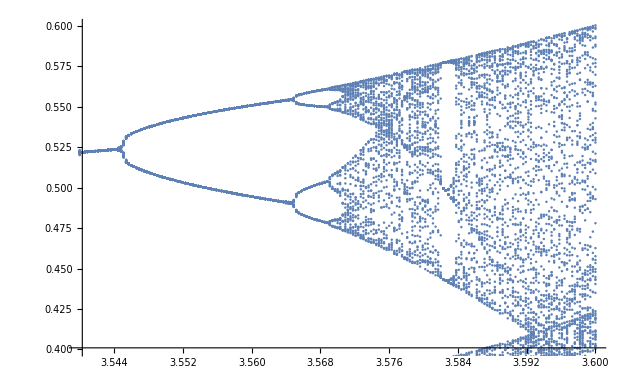

```mathematica
X={};
x0=0.4;a0 = 3.54;K = 200; PN = 200;
For[k=0,k≤K,k++,a=a0+k*(3.6-a0)/K;
For[i=1,i≤60,i++,x1=a*x0*(1-x0);  x0=x1];
For[i=61,i≤(PN+61),i++,x1=a*x0*(1-x0);AppendTo[X,{a,x1}];x0=x1]
]
ListPlot[X, PlotRange->{{a0,3.6},{0.4,0.6}}]
```

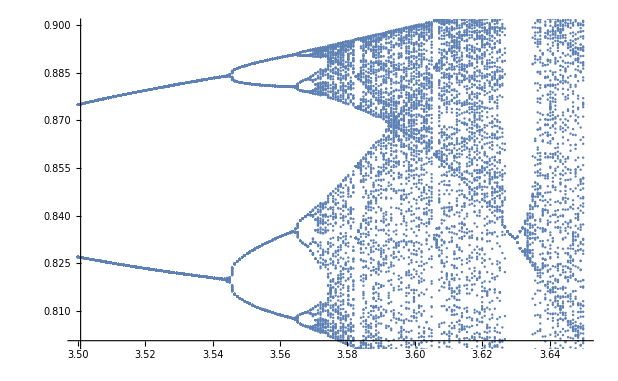

```mathematica
X={};
x0=0.4;a0 = 3.5;K = 200; PN = 200;
For[k=0,k≤K,k++,a=a0+k*(3.65-a0)/K;
For[i=1,i≤60,i++,x1=a*x0*(1-x0);  x0=x1];
For[i=61,i≤(PN+61),i++,x1=a*x0*(1-x0);AppendTo[X,{a,x1}];x0=x1]
]
ListPlot[X, PlotRange->{{a0,3.65},{0.8,0.9}}]
```